```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
h=1;
(*this is the length of the one-dimensional mesh[1]*)
L1=1.2444414542953002;
r=0.2;
cr={0.45,0.55};
```

```mathematica
(*test case 1*)
```

```mathematica
u2d[x_,y_]:=1+x^2 + 2 y^2
```

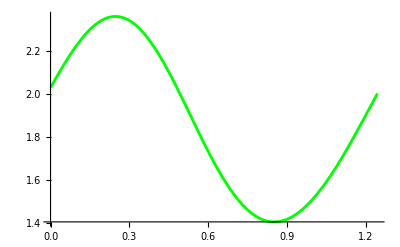

```mathematica
plot2d=Plot[u2d[cr[[1]]+r Cos[s/r],cr[[2]]+r Sin[s/r]],{s,0,L1},PlotStyle->{Green,PointSize->0.01}]
```

```mathematica
tline=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/u_line.csv"][[2;;]];
tline=Table[{tline[[i,2]],tline[[i,1]]},{i,2,Length[tline]}]
```

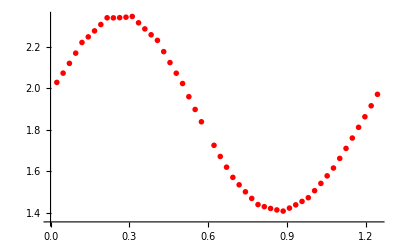

```mathematica
plottline=ListPlot[tline,PlotStyle->{Red,PointSize->0.01}]
```

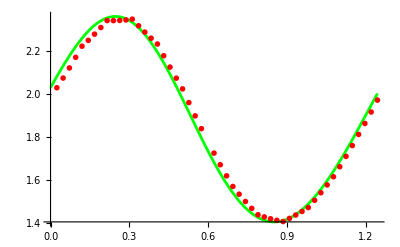

```mathematica
Show[plot2d,plottline]
```